```mathematica
Binomial[5,3]
```

10

```mathematica
Solve[Binomial[ω,n]==n^n,ω]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Binomial[ω,n]==n^n,ω]

```mathematica
Table[Floor[FindRoot[Binomial[ω,n]==n^n,{ω,n(n-1)/2}][[1]][[2]]],{n,1,10}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1,3,6,10,15,20,26,33,41,49}

```mathematica
Table[Floor[FindRoot[Binomial[ω,n]==n^n,{ω,n(n-1)/2}][[1]][[2]]],{n,1,20}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{1,3,6,10,15,20,26,33,41,49,59,69,79,91,103,116,130,144,159,175}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

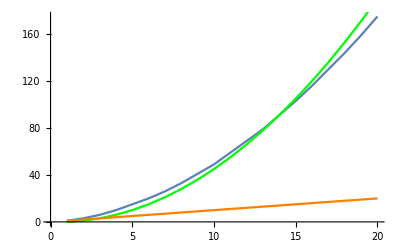

```mathematica
Show[
ListLinePlot[Table[Floor[FindRoot[Binomial[ω,n]==n^n,{ω,n(n-1)/2}][[1]][[2]]],{n,1,20}]],
ListLinePlot[Table[m(m-1)/2,{m,1,20}],PlotStyle->Green],
ListLinePlot[Table[m,{m,1,20}],PlotStyle->Orange]
]
```

```mathematica
(n^n-Binomial[ω,n])/.{n->11,ω->59}
```

5439901616

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

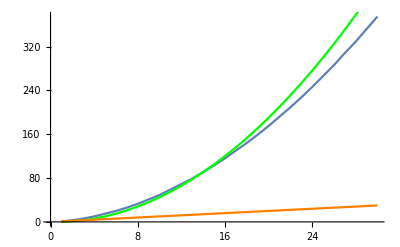

```mathematica
Show[
ListLinePlot[Table[Floor[FindRoot[Binomial[ω,n]==n^n,{ω,n(n-1)/2}][[1]][[2]]],{n,1,30}]],
ListLinePlot[Table[m(m-1)/2,{m,1,30}],PlotStyle->Green],
ListLinePlot[Table[m,{m,1,30}],PlotStyle->Orange]
]
```